## Function 1

```mathematica
f[x_]:=x^3 - x^2;
```

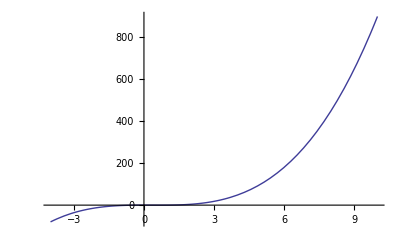

```mathematica
Plot[f[x],{x,-4,10},PlotRange->All]
```

```mathematica
nPoints = 15;
```

```mathematica
xs=Sort[RandomReal[{-4,10},nPoints]];
```

```mathematica
noise=RandomReal[{-0.5,0.5},nPoints];
```

```mathematica
ys=f[xs]+noise;
```

```mathematica
Export["/Users/matt/test1.csv",Transpose[{xs,ys}]];
```

## Function 2

```mathematica
f[x_]:=x^5 - 5*x^3;
```

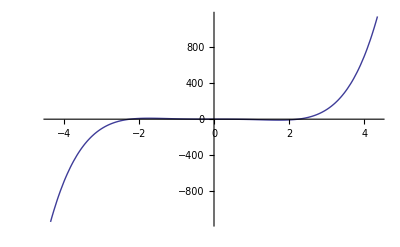

```mathematica
Plot[f[x],{x,-4.35,4.35},PlotRange->All]
```

```mathematica
nPoints=13;
```

```mathematica
xs=Sort[RandomReal[{-4.35,4.35},nPoints]];
```

```mathematica
noise=RandomReal[{-0.5,0.5},nPoints];
```

```mathematica
ys=f[xs]+noise;
```

```mathematica
Export["/Users/matt/test2.csv",Transpose[{xs,ys}]];
```

## Function 3

```mathematica
f[x_]:=x^5 - 5*x^3;
```

```mathematica
Plot[f[x],{x,-4.35,4.35},PlotRange->All]
```

-Graphics-

```mathematica
nPoints=13;
```

```mathematica
xs=Sort[RandomReal[{-4.35,4.35},nPoints]];
```

```mathematica
noise=RandomReal[{-0.5,0.5},nPoints];
```

```mathematica
ys=f[xs]+noise;
```

```mathematica
Export["/Users/matt/test2.csv",Transpose[{xs,ys}]];
```

## Function 4

```mathematica
f[x_]:=(1/x)*Sin[x];
```

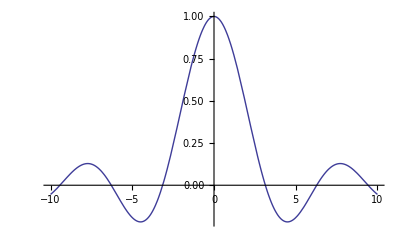

```mathematica
Plot[f[x],{x,-10,10},PlotRange->All]
```

```mathematica
nPoints=200;
```

```mathematica
xs=Sort[RandomReal[{-10,10},nPoints]];
```

```mathematica
noise=RandomReal[{-0.005,0.005},nPoints];
```

```mathematica
ys=f[xs];
```

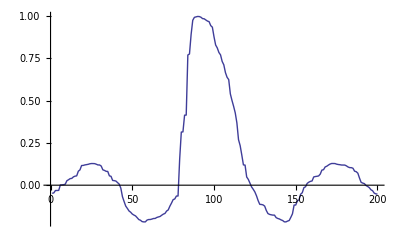

```mathematica
ListPlot[ys,PlotJoined->True]
```

```mathematica
Export["/Users/matt/test4.csv",Transpose[{xs,ys}]];
```

## Function 5

```mathematica
f[x_]:=x^2 + (x/3)^3-(2*x/9)^5;
```

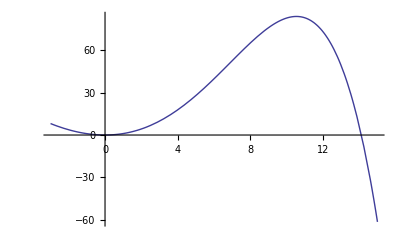

```mathematica
Plot[f[x],{x,-3,15},PlotRange->All]
```

```mathematica
nPoints=75;
```

```mathematica
xs=Sort[RandomReal[{-3.5,15},nPoints]];
```

```mathematica
noise=RandomReal[{-0.5,0.5},nPoints];
```

```mathematica
ys=f[xs]+noise;
```

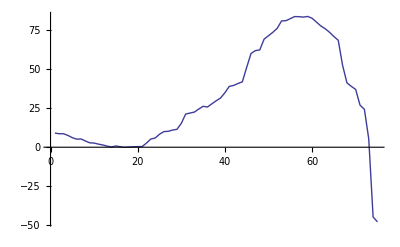

```mathematica
ListPlot[ys,PlotJoined->True]
```

```mathematica
Export["/Users/matt/test5.csv",Transpose[{xs,ys}]];
```